## Question 1

```mathematica
Needs["NumericalCalculus`"]
Clear[NDSolveAround]
NDSolveAround[eqns_,params___,opts:OptionsPattern[]]:=Module[{nn,NDRules,i,ΔΔ,X,xs,xsrules,Δs,consts,symbols,pairs,rules,efun,F,F0,G,means,errors,M,a,b,NDD,FD,outseries,MeanOutSeries,ErrorOutSeries,outrules},
(* Option settings and checks *)
nn=OptionValue["AroundReplaceOrder"];
If[(Method/.OptionValue["NDOptions"])!=EulerSum∧(Method/.OptionValue["NDOptions"])!=Method,Message[NDSolveAround::InvalidNDMethod,Method/.OptionValue["NDOptions"]],Null,Message[NDSolveAround::InvalidNDMethod,Method/.OptionValue["NDOptions"]]];
NDRules=OptionValue["NDOptions"]/.(Rule[Method,a_]->Rule[Method,EulerSum]);
(* First find constants that have error *)
consts=DeleteDuplicates[Cases[eqns,a_Around,∞]];
(* Make symbols and pair them with the consts *)
symbols=Table[Unique[],{i,1,Length[consts]}];
pairs=List@@GroupBy[{consts,symbols}ᵀ,First];
rules=MapThread[#1->#2&,{consts,symbols}];
(* Make a function which takes consts as inputs and returns eqns with these consts *)
efun=Function[Evaluate[symbols],Evaluate[eqns/.rules]];
(* Next we treat the output of NDSolve as a function, and propagate error through it based on its derivatives *)
F[vals_]:=F[vals]=NDSolveValue[efun@@vals,params,FilterRules[{opts},Options[NDSolve]]];
means=#["Value"]&/@consts;
errors=#["Uncertainty"]&/@consts;
F0=F[means];
M=Length[F0];
(* Make a function to compute finite difference expressions for higher mixed partials *)
xs=Table[Unique[X],{k,1,Length[consts]}];
Δs=Table[Unique[ΔΔ],{k,1,Length[consts]}];
xsrules=MapThread[Rule,{xs,means}];
FD[f_,{i_,n_}]:=FD[f,i]=Function[Evaluate[xs],Evaluate[(ND[f@@xs,{xs[[i]],n},xs[[i]],Sequence@@NDRules])]];
NDD[f_,l_]:=Module[{out},
out=f;
For[i=1,i<=Length[l],i++,
out=FD[out,{i,l[[i]]}]
];
out
];
(* Use these functions to compute the outvalue and outerrors *)
outseries=AroundReplace[G[Sequence@@xs],Evaluate[Table[xs[[i]]->Around[xs[[i]],Δs[[i]]],{i,1,Length[xs]}]],nn];
MeanOutSeries=outseries["Value"];
ErrorOutSeries=outseries["Uncertainty"];
outrules=MapThread[#1->#2&,{Δs,errors}];
Table[Evaluate[(Around[MeanOutSeries,ErrorOutSeries]/.{ G[__]:>F0[[m]][b],Derivative[s__][G][__]:>(NDD[a,{s}]@@means)}/.a[x__]:>F[{x}][[m]][b])/.b->##]&,{m,1,M}]/.outrules

]

Options[NDSolveAround]=Join[{
"AroundReplaceOrder"->1,
"NDOptions"->{Method->EulerSum}
},Options[NDSolve]];
NDSolveAround::InvalidNDMethod="EulerSum is currently the only supported ND method, Method → `1` will be ignored.";
```

-Graphics-

```mathematica
Partition[ToExpression@StringSplit["0 0.82 0.85
1 0.53 1.78
2 0.52 2.32
3 0.59 2.62
4 0.66 2.58
5 1.42 2.16
6 1.56 1.26
7 0.92 1.39
8 0.81 1.91
9 0.8 2.34
10 0.75 2.5
11 1 2.13
12 1.35 1.65
13 1.03 1.54
14 0.87 1.83
15 0.84 2.18
16 0.71 2.34
17 1.04 2.29
18 1.27 1.85
19 1.09 1.68
20 0.96 1.86
21 0.88 2.09
22 0.72 2.21
23 0.81 2.23
24 1.11 2.09
25 1.17 1.73
26 1.22 1.81
27 1.01 2.17
28 0.79 2.22
29 0.78 2.27
30 1.19 2.01"],3]//Iconize
```

```mathematica
data=;
```

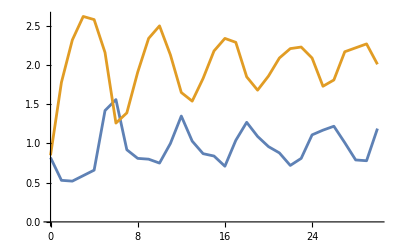

```mathematica
ListLinePlot[{data/.{t_,X_,Y_}:>{t,X},data/.{t_,X_,Y_}:>{t,Y}}]
```

```mathematica
ClearAll[SolveSystem,Xfun,Yfun]
SolveSystem[A_?NumericQ,B_?NumericQ]:=SolveSystem[A,B]=Module[{},
NDSolveValue[{
X'[t]==A + X[t]^2 Y[t]-B X[t]-X[t],
Y'[t]==B X[t]-X[t]^2 Y[t],
X[0]==data[[1,2]],
Y[0]==data[[1,3]]
},{X,Y},{t,0,31}]
]
Xfun[A_?NumericQ,B_?NumericQ,t_?NumericQ]:=SolveSystem[A,B][[1]][t]
Yfun[A_?NumericQ,B_?NumericQ,t_?NumericQ]:=SolveSystem[A,B][[2]][t]
```

```mathematica
MultiNonlinearModelFit=ResourceFunction["MultiNonlinearModelFit"];
```

```mathematica
model=MultiNonlinearModelFit[Evaluate[{data/.{t_,X_,Y_}:>{t,X},data/.{t_,X_,Y_}:>{t,Y}}],{Xfun[A,B,t],Yfun[A,B,t]},{A,B},t,Method->{"NMinimize",Method->"SimulatedAnnealing"}]
```

FittedModel[Switch[Round[n],1,Xfun[1.00842,1.99868,t],2,Yfun[1.00842,1.99868,t]]]

```mathematica
model["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
A | 1.00842 | 0.003082 | {1.00225,1.01458}
B | 1.99868 | 0.0119422 | {1.9748,2.02257}

```mathematica
{Aval,Bval}=Around@@@({Values@model["BestFitParameters"],model["ParameterErrors"]}ᵀ)
```

{1.00840.0031,1.9990.012}

```mathematica
sol=NDSolveAround[{
X'[t]==Aval + X[t]^2 Y[t]-Bval X[t]-X[t],
Y'[t]==Bval X[t]-X[t]^2 Y[t],
X[0]==data[[1,2]],
Y[0]==data[[1,3]]
},{X,Y},{t,0,31},"AroundReplaceOrder"->1];
```

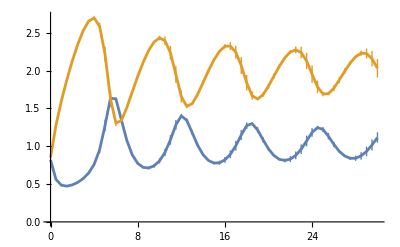

```mathematica
ListLinePlot[{Table[{t,sol[[1]][t]},{t,0,30,0.5}],Table[{t,sol[[2]][t]},{t,0,30,0.5}]}]
```

## Question 2

-Graphics-

```mathematica
A=2;
B=5;
sol=NDSolve[{
X'[t]==A + X[t]^2 Y[t]-B X[t]-X[t],
Y'[t]==B X[t]-X[t]^2 Y[t],
X[0]==1,
Y[0]==1
},{X,Y},{t,0,31}];
```

```mathematica
Xavg=1/30 NIntegrate[X[t]/.sol[[1]],{t,0,30}];
Yavg=1/30 NIntegrate[Y[t]/.sol[[1]],{t,0,30}];
```

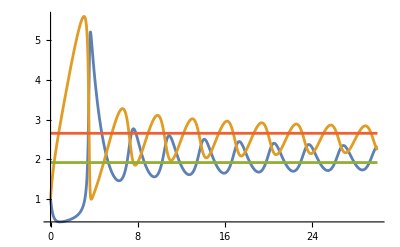

```mathematica
Plot[Evaluate[{X[t],Y[t],Xavg,Yavg}/.sol],{t,0,30},PlotRange->All]
```